```mathematica
(* Subscript[I, 2](l,L) at 2 T_c with free b.c.
=c/2 ln[(f(l/L) f((L-l)/L))/(√L f(1))]
where f(x)=Dedekindeta(ix) *)
```

```mathematica
(* Subscript[I, 2](l,L)-Subscript[I, 2](L/2,L) *)
Log[F[x,L]]-Log[F[1/2,L]]//FullSimplify
```

Log[L]/2+Log[(DedekindEta[-ⅈ (-1+x)] DedekindEta[ⅈ x])/(√L DedekindEta[ⅈ/2]^2)]

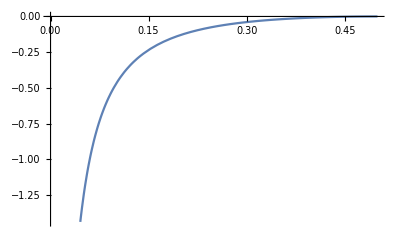

```mathematica
Clear[J,l,L,x,F,c];
(* for classical Blume-Capel model *)
c=7/10;
F[x_]:=(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2;
p=Plot[c/2 Log[F[x]],{x,0,0.5}]
```

```mathematica
(* fit data *)
```

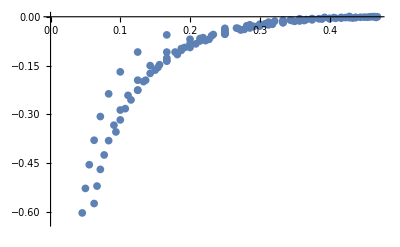

{c→0.320752}

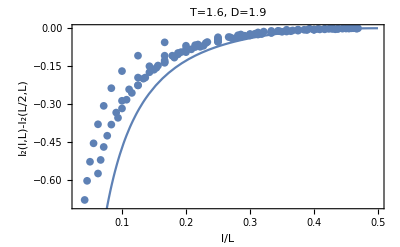

{c→0.350786}

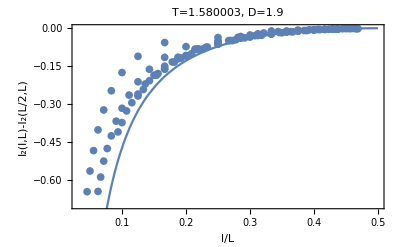

{c→0.385508}

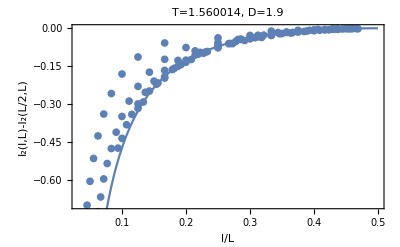

{c→0.427263}

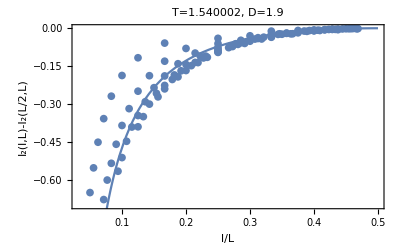

```mathematica
SetDirectory[NotebookDirectory[]];
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["tot_D1.900000_T1.600000.dat"];
a=d[[;;,3]];
b=d[[;;,4]];
data=Transpose[{a,b}];
datas=Sort[data,#1[[1]]<#2[[1]]&];
l=ListPlot[datas,DataRange->{0.2,0.5}]
ll=ListPlot[data,DataRange->{0.2,0.5}];
fit=FindFit[data,J[c,x],{c},x]
(*******************)
Clear[J,x,F,c,pfit,pactual];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}];
Show[pactual,l,PlotRange->{-0.7,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"},PlotLabel->"T=1.6, D=1.9"]
(****************************************)
Clear[a,b,c,d,data,l,fit];
d=Import["tot_D1.900000_T1.580003.dat"];
a=d[[;;,3]];
b=d[[;;,4]];
data=Transpose[{a,b}];
Sort[data,#1[[1]]<#2[[1]]&];
l=ListPlot[data];
fit=FindFit[data,J[c,x],{c},x]
(*******************)
Show[pactual,l,PlotRange->{-0.7,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"},PlotLabel->"T=1.580003, D=1.9"]
(****************************************)
Clear[a,b,c,d,data,l,fit];
d=Import["tot_D1.900000_T1.560014.dat"];
a=d[[;;,3]];
b=d[[;;,4]];
data=Transpose[{a,b}];
Sort[data,#1[[1]]<#2[[1]]&];
l=ListPlot[data];
fit=FindFit[data,J[c,x],{c},x]
(*******************)
Show[pactual,l,PlotRange->{-0.7,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"},PlotLabel->"T=1.560014, D=1.9"]
(****************************************)
Clear[a,b,c,d,data,l,fit];
d=Import["tot_D1.900000_T1.540002.dat"];
a=d[[;;,3]];
b=d[[;;,4]];
data=Transpose[{a,b}];
Sort[data,#1[[1]]<#2[[1]]&];
l=ListPlot[data];
fit=FindFit[data,J[c,x],{c},x]
(*******************)
Show[pactual,l,PlotRange->{-0.7,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"},PlotLabel->"T=1.540002, D=1.9"]
(****************************************)
```

{c→0.459701}

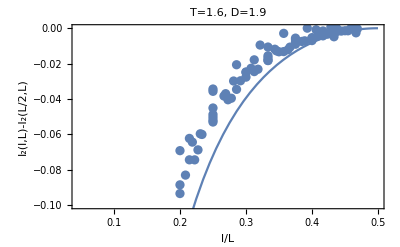

{c→0.556458}

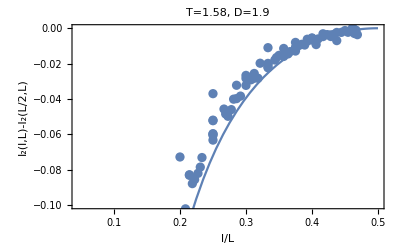

{c→0.676468}

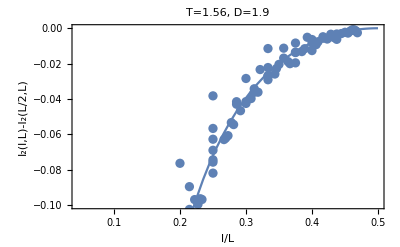

{c→0.795427}

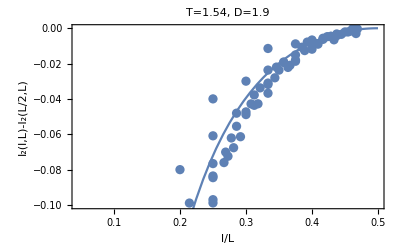

```mathematica
SetDirectory[NotebookDirectory[]];
Clear[datanew,lnew,fitnew];
datanew={{0.2,-0.069183},{0.2,-0.093417},{0.2,-0.088508},{0.20833,-0.083002},{0.21429,-0.062266},{0.21429,-0.074365},{0.21875,-0.064355},{0.22222,-0.074383},{0.22727,-0.068742},{0.23077,-0.05966},{0.23333,-0.060025},{0.25,-0.034347},{0.25,-0.048733},{0.25,-0.035653},{0.25,-0.05301},{0.25,-0.050343},{0.25,-0.051954},{0.25,-0.045075},{0.26667,-0.038306},{0.26923,-0.036993},{0.27273,-0.040424},{0.27778,-0.039557},{0.28125,-0.029828},{0.28571,-0.020625},{0.28571,-0.034545},{0.29167,-0.029693},{0.3,-0.024719},{0.3,-0.027637},{0.3,-0.024961},{0.30769,-0.022634},{0.3125,-0.024499},{0.3125,-0.017858},{0.31818,-0.023165},{0.32143,-0.0095043},{0.33333,-0.018135},{0.33333,-0.018285},{0.33333,-0.01558},{0.33333,-0.010625},{0.33333,-0.016827},{0.34375,-0.011856},{0.34615,-0.012775},{0.35,-0.013311},{0.35714,-0.0028998},{0.35714,-0.013199},{0.36364,-0.012147},{0.36667,-0.010669},{0.375,-0.0076712},{0.375,-0.0090258},{0.375,-0.0063527},{0.375,-0.0055943},{0.38462,-0.0074635},{0.38889,-0.007115},{0.39286,0.00004364},{0.4,-0.0053231},{0.4,-0.0056658},{0.4,-0.0069694},{0.40625,-0.00087438},{0.40909,-0.0043782},{0.41667,-0.0042999},{0.41667,-0.0015415},{0.42308,-0.0033832},{0.42857,0.00071151},{0.42857,-0.0028248},{0.43333,-0.0048228},{0.4375,-0.0018907},{0.4375,-0.00005513},{0.44444,-0.0016025},{0.45,-0.0014088},{0.45455,-0.0014324},{0.45833,-0.00030696},{0.46154,0.00022044},{0.46429,0.00009257},{0.46667,-0.0025895},{0.46875,-0.00032016}};
lnew=ListPlot[datanew];
fitnew=FindFit[datanew,J[c,x],{c},x]
(*******************)
Clear[J,x,F,c,pfit,pactual];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}];
Show[pactual,lnew,PlotRange->{-0.1,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"},PlotLabel->"T=1.6, D=1.9"]
(****************************************)
Clear[datanew,lnew,fitnew];
datanew={{0.2,-0.072764},{0.2,-0.10625},{0.2,-0.1059},{0.20833,-0.10208},{0.21429,-0.082804},{0.21429,-0.083105},{0.21875,-0.087816},{0.22222,-0.085542},{0.22727,-0.082009},{0.23077,-0.078488},{0.23333,-0.073083},{0.25,-0.051946},{0.25,-0.052255},{0.25,-0.036972},{0.25,-0.059766},{0.25,-0.063224},{0.25,-0.059617},{0.25,-0.060556},{0.26667,-0.045677},{0.26923,-0.048451},{0.27273,-0.049755},{0.27778,-0.046003},{0.28125,-0.040086},{0.28571,-0.032228},{0.28571,-0.039775},{0.29167,-0.038347},{0.3,-0.026656},{0.3,-0.032292},{0.3,-0.028317},{0.30769,-0.029116},{0.3125,-0.02823},{0.3125,-0.025561},{0.31818,-0.028263},{0.32143,-0.01977},{0.33333,-0.01988},{0.33333,-0.022338},{0.33333,-0.021718},{0.33333,-0.010982},{0.33333,-0.020346},{0.34375,-0.017949},{0.34615,-0.016583},{0.35,-0.01534},{0.35714,-0.011425},{0.35714,-0.015941},{0.36364,-0.014528},{0.36667,-0.013231},{0.375,-0.0080136},{0.375,-0.010942},{0.375,-0.011081},{0.375,-0.012887},{0.38462,-0.0090703},{0.38889,-0.009484},{0.39286,-0.0062217},{0.4,-0.0057614},{0.4,-0.0054673},{0.4,-0.0066005},{0.40625,-0.0092285},{0.40909,-0.006068},{0.41667,-0.0047128},{0.41667,-0.0031406},{0.42308,-0.0036042},{0.42857,-0.0046765},{0.42857,-0.0037488},{0.43333,-0.0034669},{0.4375,-0.0023879},{0.4375,-0.0069906},{0.44444,-0.0023307},{0.45,-0.0012954},{0.45455,-0.0022795},{0.45833,-0.0013675},{0.46154,0.00039255},{0.46429,-0.0029606},{0.46667,-0.0011156},{0.46875,-0.0036391}};
lnew=ListPlot[datanew];
fitnew=FindFit[datanew,J[c,x],{c},x]
Show[pactual,lnew,PlotRange->{-0.1,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"},PlotLabel->"T=1.58, D=1.9"]
(****************************************)
Clear[datanew,lnew,fitnew];
datanew={{0.2,-0.076333},{0.2,-0.12657},{0.2,-0.13857},{0.20833,-0.12118},{0.21429,-0.1024},{0.21429,-0.089531},{0.21875,-0.1174},{0.22222,-0.096848},{0.22727,-0.099516},{0.23077,-0.096376},{0.23333,-0.096785},{0.25,-0.062724},{0.25,-0.056633},{0.25,-0.038218},{0.25,-0.068975},{0.25,-0.075683},{0.25,-0.074368},{0.25,-0.081886},{0.26667,-0.062921},{0.26923,-0.06209},{0.27273,-0.060704},{0.27778,-0.053324},{0.28125,-0.054446},{0.28571,-0.04152},{0.28571,-0.042947},{0.29167,-0.046609},{0.3,-0.028391},{0.3,-0.041485},{0.3,-0.042488},{0.30769,-0.039742},{0.3125,-0.034204},{0.3125,-0.036198},{0.31818,-0.03614},{0.32143,-0.023352},{0.33333,-0.022211},{0.33333,-0.026732},{0.33333,-0.027121},{0.33333,-0.01148},{0.33333,-0.02911},{0.34375,-0.025877},{0.34615,-0.022777},{0.35,-0.020427},{0.35714,-0.011274},{0.35714,-0.016884},{0.36364,-0.018839},{0.36667,-0.020024},{0.375,-0.0083734},{0.375,-0.013738},{0.375,-0.013546},{0.375,-0.019566},{0.38462,-0.01319},{0.38889,-0.011562},{0.39286,-0.0051057},{0.4,-0.0063796},{0.4,-0.0083303},{0.4,-0.01263},{0.40625,-0.0092714},{0.40909,-0.007628},{0.41667,-0.0056561},{0.41667,-0.0048139},{0.42308,-0.0061065},{0.42857,-0.0033816},{0.42857,-0.0037978},{0.43333,-0.0052624},{0.4375,-0.003253},{0.4375,-0.0062771},{0.44444,-0.0030047},{0.45,-0.0022952},{0.45455,-0.0027415},{0.45833,-0.0014914},{0.46154,-0.00085216},{0.46429,-0.00098503},{0.46667,-0.0015585},{0.46875,-0.0025404}};
fitnew=FindFit[datanew,J[c,x],{c},x]
lnew=ListPlot[datanew];
(*******************)
Show[pactual,lnew,PlotRange->{-0.1,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"},PlotLabel->"T=1.56, D=1.9"]
(****************************************)
Clear[datanew,lnew,fitnew];
datanew={{0.2,-0.079918},{0.2,-0.14344},{0.2,-0.16803},{0.20833,-0.14843},{0.21429,-0.13119},{0.21429,-0.098802},{0.21875,-0.1424},{0.22222,-0.1111},{0.22727,-0.11702},{0.23077,-0.10921},{0.23333,-0.1161},{0.25,-0.083501},{0.25,-0.060804},{0.25,-0.039923},{0.25,-0.076489},{0.25,-0.09689},{0.25,-0.084442},{0.25,-0.098735},{0.26667,-0.075919},{0.26923,-0.070003},{0.27273,-0.072346},{0.27778,-0.062015},{0.28125,-0.06753},{0.28571,-0.055404},{0.28571,-0.048007},{0.29167,-0.061311},{0.3,-0.029912},{0.3,-0.04728},{0.3,-0.048795},{0.30769,-0.04275},{0.3125,-0.037696},{0.3125,-0.043556},{0.31818,-0.0427},{0.32143,-0.033696},{0.33333,-0.023648},{0.33333,-0.031003},{0.33333,-0.036729},{0.33333,-0.011433},{0.33333,-0.031771},{0.34375,-0.028011},{0.34615,-0.021959},{0.35,-0.023681},{0.35714,-0.019067},{0.35714,-0.019366},{0.36364,-0.022144},{0.36667,-0.020944},{0.375,-0.008845},{0.375,-0.015073},{0.375,-0.018661},{0.375,-0.017997},{0.38462,-0.010728},{0.38889,-0.012628},{0.39286,-0.0078211},{0.4,-0.0066369},{0.4,-0.009264},{0.4,-0.011844},{0.40625,-0.0086357},{0.40909,-0.0090053},{0.41667,-0.0056622},{0.41667,-0.0062838},{0.42308,-0.0047554},{0.42857,-0.0045591},{0.42857,-0.0046067},{0.43333,-0.0065413},{0.4375,-0.0032374},{0.4375,-0.0041959},{0.44444,-0.0034465},{0.45,-0.0020806},{0.45455,-0.0021063},{0.45833,-0.0016122},{0.46154,-0.0002735},{0.46429,0.00011596},{0.46667,-0.002989},{0.46875,-0.00036905}};
lnew=ListPlot[datanew];
fitnew=FindFit[datanew,J[c,x],{c},x]
Show[pactual,lnew,PlotRange->{-0.1,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"},PlotLabel->"T=1.54, D=1.9"]
(****************************************)
Clear[datanew,lnew,fitnew];
```

```mathematica
(* c extrapolation to L->∞*)
```

```mathematica
(* l/L=1/4 *)
dat3={{1/8,bb8[[3]]},{1/16,bb16[[5]]},{1/24,bb24[[7]]}}
```

{{1/8,-0.0359068},{1/16,-0.0654667},{1/24,-0.0752548}}

```mathematica
(* l/L=1/4 *)
Clear[lbL,f,m,i,dat];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL3=1.0/4;
J[0.7,lbL3]
f=FindFit[dat3,m x +i,{m,i},x];
v3=i/.f[[2]];
line3=Fit[dat3,{1,x},x](* x = 1/L *)
```

-0.0719068

-0.0949588+0.472356 x

```mathematica
(* l/L=1/5 *)
dat4={{1/10,bb10[[3]]},{1/20,bb20[[5]]},{1/30,bb30[[7]]}}
```

{{1/10,-0.0720259},{1/20,-0.12363},{1/30,-0.129087}}

```mathematica
(* l/L=1/5 *)
Clear[lbL,f,m,i,dat];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL4=1.0/5;
J[0.7,lbL4]
f=FindFit[dat4,m x +i,{m,i},x];
v4=i/.f[[2]];
line4=Fit[dat4,{1,x},x](* x = 1/L *)
```

-0.1282

-0.163039+0.896577 x

```mathematica
(* l/L=2/5 *)
dat5={{1/10,bb10[[5]]},{1/20,bb20[[9]]},{1/30,bb30[[13]]}}
```

{{1/10,-0.00597281},{1/20,-0.00839806},{1/30,-0.00628211}}

```mathematica
(* l/L=2/5 *)
Clear[lbL,f,m,i,dat];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL5=2.0/5;
J[0.7,lbL5]
f=FindFit[dat5,m x +i,{m,i},x];
v5=i/.f[[2]];
line5=Fit[dat5,{1,x},x](* x = 1/L *)
```

-0.00813531

-0.00500212-0.0095992 x

```mathematica
(* l/L=1/8 *)
dat6={{1/8,bb8[[2]]},{1/16,bb16[[3]]},{1/24,bb24[[4]]}}
```

{{1/8,-0.108742},{1/16,-0.221975},{1/24,-0.292863}}

```mathematica
(* l/L=1/8 *)
Clear[lbL,f,m,i,dat];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL6=1.0/8;
J[0.7,lbL6]
f=FindFit[dat6,m x +i,{m,i},x];
v6=i/.f[[2]];
line6=Fit[dat6,{1,x},x](* x = 1/L *)
```

0.35 Log[(DedekindEta[ⅈ (1-lbL)] DedekindEta[ⅈ lbL])/DedekindEta[ⅈ/2]^2]

-0.369626+2.11767 x

```mathematica
(* l/L=1/10 *)
dat7={{1/10,bb10[[2]]},{1/20,bb20[[3]]},{1/30,bb30[[4]]}}
```

```mathematica
{{1/10,-0.17336479},{1/20,-0.34148654},{1/30,-0.42518273}}
```

{{1/10,-0.173365},{1/20,-0.341487},{1/30,-0.425183}}

```mathematica
(* l/L=1/10 *)
Clear[lbL,i,m,dat,f];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL7=1.0/10;
J[0.7,lbL7]
f=FindFit[dat7,m x +i,{m,i},x];
v7=i/.f[[2]];
line7=Fit[dat7,{1,x},x](* x = 1/L *)
```

-0.473124

-0.538328+3.68154 x

```mathematica
(* l/L=3/10 *)
dat8={{1/10,bb10[[4]]},{1/20,bb20[[7]]},{1/30,bb30[[10]]}}
```

{{1/10,-0.026917},{1/20,-0.0414687},{1/30,-0.0390205}}

```mathematica
(* l/L=3/10 *)
Clear[m,i,f];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL8=3.0/10;
J[0.7,lbL8]
f=FindFit[dat8,m x +i,{m,i},x];
v8=i/.f[[2]];
line8=Fit[dat8,{1,x},x](* x = 1/L *)
```

-0.0393431

-0.048441+0.206818 x

```mathematica
(* l/L=3/8 *)
dat9={{1/8,bb8[[4]]},{1/16,bb16[[7]]},{1/24,bb24[[10]]}}
```

{{1/8,-0.00802358},{1/16,-0.011606},{1/24,-0.0140521}}

```mathematica
(* l/L=3/8 *)
Clear[m,i,f];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL9=3.0/8;
J[0.7,lbL9]
f=FindFit[dat9,m x +i,{m,i},x];
v9=i/.f[[2]];
line9=Fit[dat9,{1,x},x](* x = 1/L *)
```

-0.013153

-0.0164885+0.0688752 x

```mathematica
(* l/L=1/12 *)
dat10={{1/12,bb12[[2]]},{1/24,bb24[[3]]}}
```

{{1/12,-0.248259},{1/24,-0.467504}}

```mathematica
Clear[m,i,f];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL10=1.0/12;
J[0.7,lbL10]
f=FindFit[dat10,m x +i,{m,i},x];
v10=i/.f[[2]];
line10=Fit[dat10,{1,x},x](* x = 1/L *)
```

-0.625881

-0.68675+5.26189 x

```mathematica
(* l/L=5/12 *)
dat11={{1/12,bb12[[6]]},{1/24,bb24[[11]]}}
```

{{1/12,-0.00470166},{1/24,-0.00603443}}

```mathematica
dat11={{1/12,-0.00470166},{1/24,-0.00603443}};
```

```mathematica
(* l/L=5/12 *)
Clear[f,i,m];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL11=5.0/12;
J[0.7,lbL11]
f=FindFit[dat11,m x +i,{m,i},x];
v11=i/.f[[2]];
line11=Fit[dat11,{1,x},x](* x = 1/L *)
```

-0.00554708

-0.0073672+0.0319865 x

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.100000_D1.900000_T1.560014.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r1=0.100000;
J[0.7,r1]
f=FindFit[data,m x +i,{m,i},x];
v21=i/.f[[2]];
line11=Fit[data,{1,x},x](* x = 1/L *)
```

-0.473124

-0.54875+3.71182 x

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.166670_D1.900000_T1.560014.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r2=0.166670;
J[0.7,r2]
f=FindFit[data,m x +i,{m,i},x];
v22=i/.f[[2]]
```

-0.190529

-0.258771

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.200000_D1.900000_T1.560014.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r3=0.200000;
J[0.7,r3]
f=FindFit[data,m x +i,{m,i},x];
v23=i/.f[[2]]
```

-0.1282

-0.167206

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.250000_D1.900000_T1.560014.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r4=0.250000;
J[0.7,r4]
f=FindFit[data,m x +i,{m,i},x];
v24=i/.f[[2]]
```

-0.0719068

-0.0807353

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.250000_D1.900000_T1.560014.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r5=0.250000;
J[0.7,r5]
f=FindFit[data,m x +i,{m,i},x];
v25=i/.f[[2]]
```

-0.0719068

-0.0807353

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.300000_D1.900000_T1.560014.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r6=0.300000;
J[0.7,r6]
f=FindFit[data,m x +i,{m,i},x];
v26=i/.f[[2]]
```

-0.0393431

-0.0496829

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.333330_D1.900000_T1.560014.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r7=0.333330;
J[0.7,r7]
f=FindFit[data,m x +i,{m,i},x];
v27=i/.f[[2]]
```

-0.0252299

-0.0346664

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.375000_D1.900000_T1.560014.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r8=0.375000;
J[0.7,r8]
f=FindFit[data,m x +i,{m,i},x];
v28=i/.f[[2]]
```

-0.013153

-0.0181709

{c→0.834936}

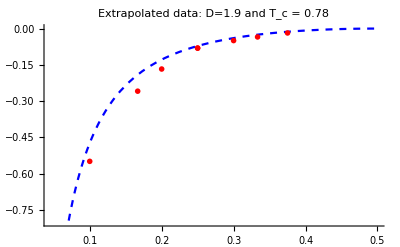

```mathematica
Clear[J,pactual,c,dataextr,plotextr];
marker1=Graphics[{Disk[]}];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}, PlotStyle->{Dashed, Blue}];
dataextr={{r1,v21},{r2,v22},{r3,v23},{ r4 ,v24},{r5,v25},{r6,v26},{r7,v27},{r8,v28}};
FindFit[dataextr,J[c,x],{c},x]
plotextr=ListPlot[dataextr,PlotStyle->Red,PlotMarkers->{marker1,.03}];
Show[{pactual,plotextr},PlotRange->{-0.8,0},PlotLabel->"Extrapolated data: D=1.9 and T_c = 0.78"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.100000_D1.900000_T1.580003.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r1=0.100000;
J[0.7,r1]
f=FindFit[data,m x +i,{m,i},x];
v11=i/.f[[2]];
line11=Fit[data,{1,x},x](* x = 1/L *)
```

-0.473124

-0.467755+2.93464 x

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.166670_D1.900000_T1.580003.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r2=0.166670;
J[0.7,r2]
f=FindFit[data,m x +i,{m,i},x];
v12=i/.f[[2]]
```

-0.190529

-0.210891

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.200000_D1.900000_T1.580003.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r3=0.200000;
J[0.7,r3]
f=FindFit[data,m x +i,{m,i},x];
v13=i/.f[[2]]
```

-0.1282

-0.131739

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.250000_D1.900000_T1.580003.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r4=0.250000;
J[0.7,r4]
f=FindFit[data,m x +i,{m,i},x];
v14=i/.f[[2]]
```

-0.0719068

-0.0622172

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.250000_D1.900000_T1.580003.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r5=0.250000;
J[0.7,r5]
f=FindFit[data,m x +i,{m,i},x];
v15=i/.f[[2]]
```

-0.0719068

-0.0622172

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.300000_D1.900000_T1.580003.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r6=0.300000;
J[0.7,r6]
f=FindFit[data,m x +i,{m,i},x];
v16=i/.f[[2]]
```

-0.0393431

-0.0375191

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.333330_D1.900000_T1.580003.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r7=0.333330;
J[0.7,r7]
f=FindFit[data,m x +i,{m,i},x];
v17=i/.f[[2]]
```

-0.0252299

-0.0235679

```mathematica
SetDirectory[NotebookDirectory[]];
(*"L \ x \ x/L \ 1/L \ I2shifted \ errorbar"*)
Clear[Dval];
Dval=1.9;
(***********************)
Clear[a,b,c,d,data,l,fit];
d=Import["extra_x0.375000_D1.900000_T1.580003.dat"];
a=d[[;;,4]];
b=d[[;;,5]];
data=Transpose[{a,b}];
Clear[f,i,m,x,r];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
r8=0.375000;
J[0.7,r8]
f=FindFit[data,m x +i,{m,i},x];
v18=i/.f[[2]]
```

-0.013153

-0.0133048

{c→0.700697}

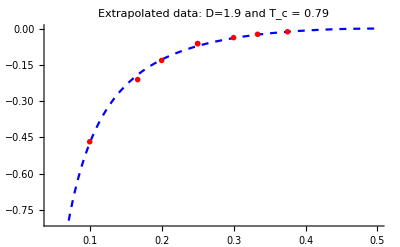

```mathematica
Clear[J,pactual,c,dataextr,plotextr];
marker1=Graphics[{Disk[]}];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}, PlotStyle->{Dashed, Blue}];
dataextr={{r1,v11},{r2,v12},{r3,v13},{ r4 ,v14},{r5,v15},{r6,v16},{r7,v17},{r8,v18}};
FindFit[dataextr,J[c,x],{c},x]
plotextr=ListPlot[dataextr,PlotStyle->Red,PlotMarkers->{marker1,.03}];
Show[{pactual,plotextr},PlotRange->{-0.8,0},PlotLabel->"Extrapolated data: D=1.9 and T_c = 0.79"]
```